```mathematica
(*LT Version 2022_03_08*)
(* a priori model parameters *)
(**)
(* add. gen. var. trait *)
GT=0.5; 
(* add. gen. var. preference *)
GP=0.1;
(* add. gen. COvar. trait/preference *) 
BTP=0.01; 
(* mate choice trait intensity ? *)
a=0.03;  
(* survivorship trait cost *)
c=0.02;
(* survivorship preference cost *) b=0.0;
```

```mathematica
(* one-generation difference equations *)
newT[t_,p_,gt_,btp_,a_,b_,c_]:=1/2*gt*(a*p-2*c*t)-btp*(b*p)+t;
newP[t_, p_,btp_,gp_,a_,b_,c_]:=1/2*btp*(a*p-2*c*t)-gp*(b*p)+p;

fixedNewT[t_,p_]:=newT[t,p,GT,BTP,a,b,c];
fixedNewP[t_,p_]:=newP[t,p,BTP,GP,a,b,c];
```

```mathematica
(* Get vectors across combinations of {t,p} to {newT, newP} *)
minT=0;
maxT=1;
incT=0.03;
minP=0;
maxP=1;
incP=0.03;

DynamicModule[{BTP},{Slider[Dynamic[BTP], {0,1,0.01}],
solutions=Flatten[Table[{{p,t}, {newP[t,p, BTP, GP, a, b,c],newT[t,p,GT,BTP,a,b,c]}}, {t,minT,maxT,incT},{p,minP,maxP,incP}],1];
inputs=ListPlot[solutions[[All,1]]];
vectors=Graphics[{Arrowheads[0.02],Arrow[solutions]}];
Show[inputs,vectors]}]
```

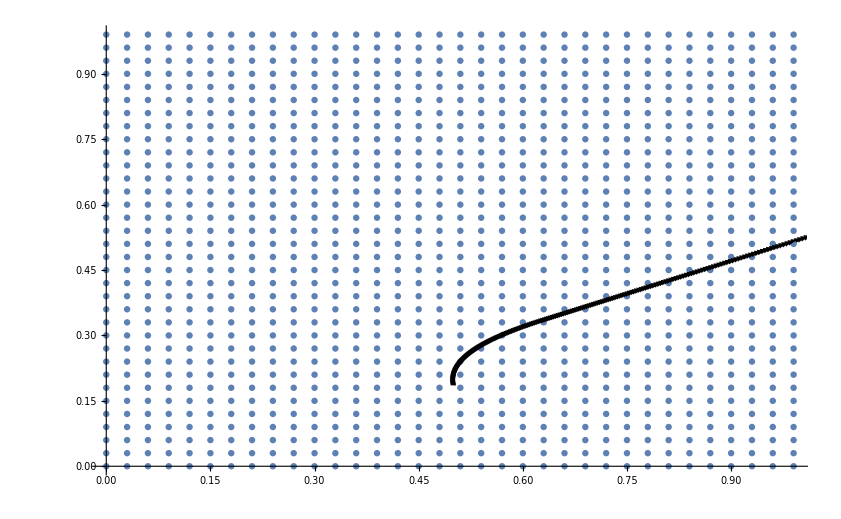

```mathematica
(* Test of tracking individual inter-generational trajectories where trait/preference covariance itself evolves *)
(* the dumbest possible update function: Btp just increases by a tiny bit every generation *)
NGEN=10000;

solutions= {{{0,0},{0,0}}};
t=0.2;
p=0.5;
btp=BTP;
gt=GT;
gp=GP;
q=0.01;

For[g=0,g<NGEN,g++,
nt=newT[t,p,gt,btp,a,b,c];
np=newP[t,p,btp,gp,a,b,c];
endValues={nt,np};

AppendTo[solutions, {{p,t},{np,nt}}];
t=nt;
p=np;

btp=btp+q*(np/p);
If[btp>1.0,btp=1.0];
]

solutions=Drop[solutions,1];
vectors=Graphics[{Arrowheads[0.01],Arrow[solutions]}, PlotRange->{{0,0},{1,1}}];
Show[inputs,vectors]
```